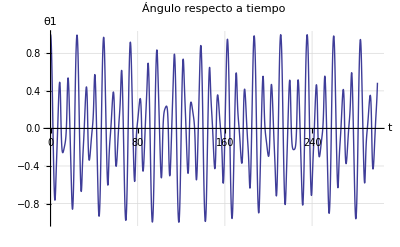

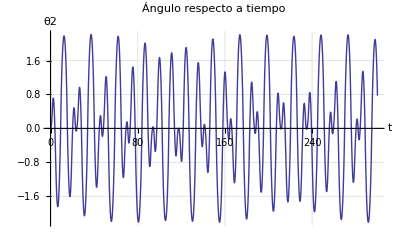

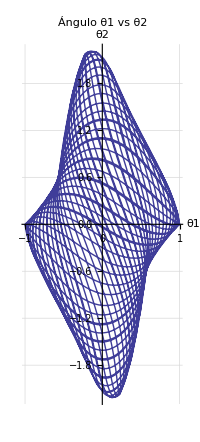

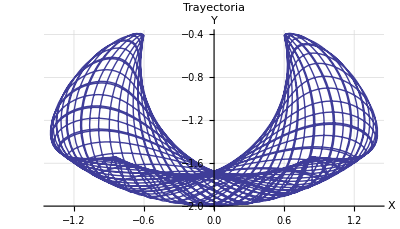

```mathematica
(* Resuelve ecuaciones diferenciales del doble péndulo numéricamente. *)
tMax =300;
With[{m1=10.0,
m2=5,
l=20.0,
g=9.81},sol = NDSolve[{θ1''[t]==(-g*( 2*m1+m2 )*Sin[θ1[t]]-m2*g*Sin[θ1[t]-2*θ2[t]]-2*Sin[θ1[t]-θ2[t]]*m2*( l*(θ2'[t]^2 )+( θ1'[t]^2 )*Cos[θ1[t]-θ2[t]] ))/(l*(2*m1+m2-m2*Cos[2*(θ1[t]-θ2[t])])), θ2''[t]==(2*Sin[θ1[t]-θ2[t]]*(g*(m1+m2)*Cos[θ1[t]]+l*((θ2'[t]^2)*m2*Cos[θ1[t]-θ2[t]]+(θ1'[t]^2)*(m1+m2))))/(l*(2*m1+m2-m2*Cos[2*(θ1[t]-θ2[t])])),
θ1[0] == 1, θ2[0] == 0, θ2'[0] == 0, θ1'[0] == 0},{θ1,θ2},{t,0,tMax},AccuracyGoal->40]];

Plot[Evaluate[θ1[t]/.sol],{t,0,tMax},PlotRange->All,AxesLabel->{Style["t", 15], Style["θ1", 15]}, GridLines->Automatic,PlotLabel->Style["Ángulo respecto a tiempo", 15]]
Plot[Evaluate[θ2[t]/.sol],{t,0,tMax},PlotRange->All,AxesLabel->{Style["t", 15], Style["θ2", 15]}, GridLines->Automatic,PlotLabel->Style["Ángulo respecto a tiempo", 15]]
ParametricPlot[Evaluate[{θ1[t],θ2[t]}/.sol],{t,0,tMax},AxesLabel->{Style["θ1", 15], Style["θ2", 15]}, GridLines->Automatic,PlotLabel->Style["Ángulo θ1 vs θ2", 15]]
ParametricPlot[Evaluate[{Sin[θ1[t]]+Sin[θ2[t]],-Cos[θ1[t]]-Cos[θ2[t]]}/.sol],{t,0,tMax},AxesLabel->{Style["X", 15], Style["Y", 15]},PlotLabel->Style["Trayectoria", 15], GridLines->Automatic]
```